```mathematica
Animating flow in phase space
Didi Park - Computational Physics, Period 6
```

```mathematica
(*Create 20 random points, pair the numbers using transpose. Rerun to get a new set of points.*)
r1 = RandomReal[{-4,4},{100}];
r2 = RandomReal[{-4,4},{100}];
pos = Transpose[{ r1,r2}];
```

```mathematica
(*Feed points to NDSolve. You can change the set of differential equations here.*)
makePoints = Function[{a},NDSolve[{v'[t]==-4x[t], x'[t]==v[t],x[0]==a[[1]],v[0]== a[[2]]},{x,v},{t,0,10}]];
(*Animate the flow of points*)
Animate[
Show[
StreamPlot[{v,-4x},{x,-4,4},{v,-4,4}],(*StreamPlot the vector field *)
Graphics[{PointSize->Large,Red,
		Point[
		Table[{ x[t]/.First[makePoints[pos[[c]]]],v[t]/.First[makePoints[pos[[c]]]]}
			,{c,1,100}]],PlotRange->{{-4,4},{-4,4}} ,AspectRatio->GoldenRatio}
]
],{t,0,1},AnimationRunning->False
]
```

```mathematica
s = NDSolve[{v'[t]==-4x[t], x'[t]==v[t],x[0]==2,v[0]== 2},{x,v},{t,0,10}]
```

{{x→InterpolatingFunction[{{0.,10.}},<>],v→InterpolatingFunction[{{0.,10.}},<>]}}

```mathematica
x[2.5]/.First[s]
```

-0.3916

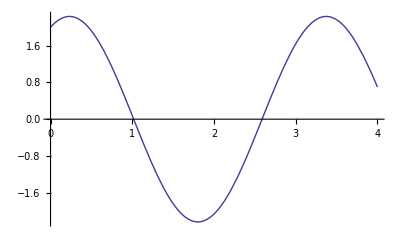

```mathematica
Plot[x[t]/.First[s], {t,0,4}]
```

```mathematica
Grap
```

```mathematica
Map[
```

```mathematica
InputForm[Table[{ x[t]/.First[makePoints[pos[[c]]]],v[t]/.First[makePoints[pos[[c]]]]}
			,{c,1,20}]]
```